# ConvexificationScaling

## Empirical scaling of convexification time under polygon averaging

## Purpose

This notebook supports the Chapter 4 numerical study of convexification time. It generates random centered polygons, applies the averaging dynamics, records the first strictly convex iterate, summarizes retained trials, fits quadratic scaling laws in the number of vertices, studies dependence on alpha, and compares the empirical time scale with the spectral-gap prediction.

All executable mathematics appears in ordinary Wolfram Language Input cells. Explanatory prose appears in ordinary Text cells. This notebook contains no hand-authored BoxData, RowBox, or FormBox expressions.

## 1. Averaging dynamics and convexity criterion

```mathematica
ClearAll["Global`*"];

applyA[p_List, alpha_?NumericQ] :=
  (1 - alpha) N[p] + alpha RotateLeft[N[p]];

centerPolygon[p_List] :=
  N[p] - Mean[N[p]];

edges[p_List] :=
  RotateLeft[N[p]] - N[p];

signedTurnAreas[p_List] := Module[{e, n},
  e = edges[p];
  n = Length[e];
  Chop@N@Table[
    Im[Conjugate[e[[j]]] e[[Mod[j, n] + 1]]],
    {j, 1, n}
  ]
];

strictlyConvexCCWQ[p_List, tol_?NumericQ] := Module[{a},
  a = signedTurnAreas[p];
  TrueQ[Min[a] > tol]
];

strictlyConvexCWQ[p_List, tol_?NumericQ] := Module[{a},
  a = signedTurnAreas[p];
  TrueQ[Max[a] < -tol]
];

strictlyConvexQ[p_List, tol_?NumericQ] :=
  TrueQ[strictlyConvexCCWQ[p, tol] || strictlyConvexCWQ[p, tol]];
```

## 2. Random polygon models

```mathematica
randomCenteredPolygon[
n_Integer?Positive,
seed_Integer
]:=Module[{p},
SeedRandom[seed];
p=
RandomReal[{-1,1},n]+
I RandomReal[{-1,1},n];
centerPolygon[p]
];
```

```mathematica
randomHalfNormalPolygon[
n_Integer?Positive,
seed_Integer,
sigma_?Positive
]:=Module[{radii,angles,p},
SeedRandom[seed];

radii=RandomVariate[
HalfNormalDistribution[sigma],
n
];

angles=RandomReal[
{0,2 Pi},
n
];

p=radii Exp[I angles];

centerPolygon[p]
];

randomHalfNormalPolygon[
n_Integer?Positive,
seed_Integer
]:=
randomHalfNormalPolygon[n,seed,1.0];
```

## 3. First strictly convex iterate

```mathematica
Clear[firstStrictConvexTime];

firstStrictConvexTime[p_List, alpha_?NumericQ] :=
  firstStrictConvexTime[p, alpha, 1000, 10^-10];

firstStrictConvexTime[p_List, alpha_?NumericQ, maxM_Integer?NonNegative] :=
  firstStrictConvexTime[p, alpha, maxM, 10^-10];

firstStrictConvexTime[p_List, alpha_?NumericQ, maxM_Integer?NonNegative, tol_?NumericQ] := Module[
  {iterate, m},
  iterate = N[p];
  For[m = 0, m <= maxM, m++,
    If[TrueQ[strictlyConvexQ[iterate, tol]], Return[m]];
    iterate = applyA[iterate, alpha];
  ];
  Missing["NotFound", maxM]
];
```

```mathematica
polygonAtTime[
p_List,
alpha_?NumericQ,
m_Integer?NonNegative
]:=
Nest[
applyA[#,alpha]&,
N[p],
m
];
```

```mathematica
pExample = randomHalfNormalPolygon[15,2026,1.0];
alphaExample = 0.35;
convexificationTimeExample = firstStrictConvexTime[pExample, alphaExample, 1000];
convexificationTimeExample
```

17

## 4. Trial-level experiment

```mathematica
convexificationTrial[
  generator_,
  ensembleName_String,
  n_Integer?Positive,
  alpha_?NumericQ,
  seed_Integer,
  maxM_Integer?NonNegative
] := Module[{p, time},

  p = generator[n, seed];

  time = firstStrictConvexTime[
    p,
    alpha,
    maxM
  ];

  <|
    "ensemble" -> ensembleName,
    "n" -> n,
    "alpha" -> alpha,
    "seed" -> seed,
    "time" -> time,
    "retained" -> IntegerQ[time]
  |>
];
```

```mathematica
Dataset@{
convexificationTrial[
randomCenteredPolygon,
"SquareCoordinates",
12,
alphaExample,
3001,
1000
],
convexificationTrial[
randomHalfNormalPolygon,
"HalfNormalRadial",
12,
alphaExample,
3001,
1000
]
}
```

## 5. Final matched experiment grid

```mathematica
runConvexificationExperiment[
  generator_,
  ensembleName_String,
  nValues_List,
  alpha_?NumericQ,
  trials_Integer?Positive,
  maxM_Integer?NonNegative,
  seedBase_Integer
] := Flatten@Table[

  convexificationTrial[
    generator,
    ensembleName,
    n,
    alpha,
    seedBase + 10000 n + trial,
    maxM
  ],

  {n, nValues},
  {trial, 1, trials}
];
```

The evaluated pilot used n = 10, 15, 20 with 10 trials per ensemble and retained every trial under a cutoff of 3000 iterations. The final experiment below uses n = 10, 15, ..., 100 and 250 trials per n and ensemble. The cutoff is raised to 5000 because the pilot means already increase rapidly with n and the Chapter 4 theory predicts quadratic growth. Reevaluate this cell and every subsequent section so that the displayed summaries and fits replace the pilot outputs.

```mathematica
experimentParameters = <|
  "nValues" -> Range[10, 100, 5],
  "Alpha" -> 0.35,
  "Trials" -> 250,
  "MaxIterations" -> 5000,
  "SeedBase" -> 50000
|>;

nValuesComparison = experimentParameters["nValues"];
alphaComparison = experimentParameters["Alpha"];
trialsComparison = experimentParameters["Trials"];
maxMComparison = experimentParameters["MaxIterations"];
seedBaseComparison = experimentParameters["SeedBase"];

squareData =
  runConvexificationExperiment[
    randomCenteredPolygon,
    "SquareCoordinates",
    nValuesComparison,
    alphaComparison,
    trialsComparison,
    maxMComparison,
    seedBaseComparison
  ];
  
  halfNormalData =
  runConvexificationExperiment[
    randomHalfNormalPolygon,
    "HalfNormalRadial",
    nValuesComparison,
    alphaComparison,
    trialsComparison,
    maxMComparison,
    seedBaseComparison
  ];
  
  comparisonData =
  Join[squareData, halfNormalData];

  Dataset@{
    <|"parameter" -> "n values", "value" -> nValuesComparison|>,
    <|"parameter" -> "alpha", "value" -> alphaComparison|>,
    <|"parameter" -> "trials per n and ensemble", "value" -> trialsComparison|>,
    <|"parameter" -> "maximum iterations", "value" -> maxMComparison|>,
    <|"parameter" -> "total trials", "value" ->
      2 Length[nValuesComparison] trialsComparison|>
  }
```

## 6. Retained-trial summaries

```mathematica
summarizeByEnsembleAndN[data_List] := Module[
  {groups},

  groups = GroupBy[
    data,
    {#ensemble, #n} &
  ];

  KeyValueMap[
    Function[{key, rows},
      Module[{times, retainedCount, totalCount},

        times =
          Cases[
            rows[[All, "time"]],
            _Integer
          ];

        retainedCount = Length[times];
        totalCount = Length[rows];

        <|
          "ensemble" -> key[[1]],
          "n" -> key[[2]],
          "trials" -> totalCount,
          "retained" -> retainedCount,
          "retentionRate" ->
            N[retainedCount/totalCount],

          "meanTime" ->
            If[
              retainedCount > 0,
              Mean[times],
              Missing["NoRetainedTrials"]
            ],

          "medianTime" ->
            If[
              retainedCount > 0,
              Median[times],
              Missing["NoRetainedTrials"]
            ],

          "standardDeviation" ->
            If[
              retainedCount > 1,
              StandardDeviation[times],
              Missing["InsufficientData"]
            ],

          "standardError" ->
            If[
              retainedCount > 1,
              StandardDeviation[times]/
                Sqrt[retainedCount],
              Missing["InsufficientData"]
            ]
        |>
      ]
    ],
    groups
  ]
];
```

```mathematica
comparisonSummary =
  summarizeByEnsembleAndN[
    comparisonData
  ];

Dataset[comparisonSummary]
```

## 7. Mean convexification time versus n

```mathematica
meanDataByEnsemble =
  GroupBy[
    Cases[
      comparisonSummary,
      row_ /; NumericQ[row["meanTime"]] :>
        {
          row["ensemble"],
          row["n"],
          row["meanTime"]
        }
    ],
    First -> Rest
  ];
```

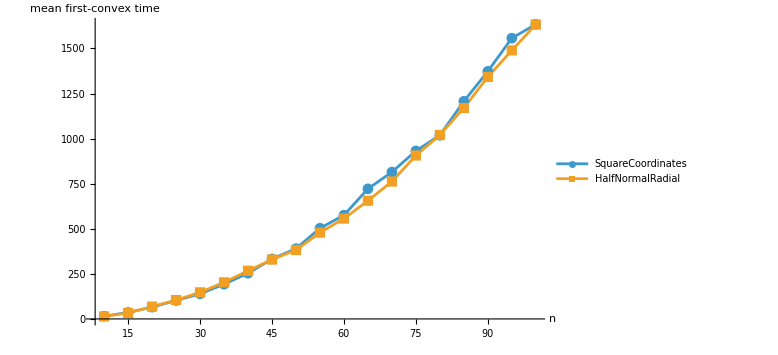

```mathematica
ListPlot[
  Values[meanDataByEnsemble],
  Joined -> True,
  PlotMarkers -> Automatic,
  PlotLegends -> Keys[meanDataByEnsemble],
  AxesLabel -> {
    "n",
    "mean first-convex time"
  },
  PlotRange -> All,
  ImageSize -> Large
]
```

## 8. Quadratic regression

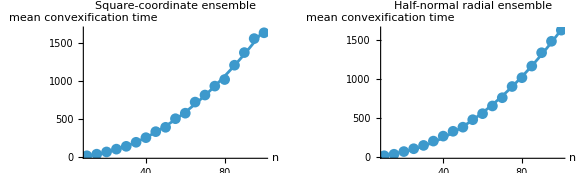

```mathematica
meanTimeDataByEnsemble=GroupBy[
Cases[
comparisonSummary,
row_/;NumericQ[row["meanTime"]]:>
{row["ensemble"],row["n"],row["meanTime"]}
],
First->Rest
];

squareMeanTimeData=Lookup[
meanTimeDataByEnsemble,
"SquareCoordinates",
{}
];

halfNormalMeanTimeData=Lookup[
meanTimeDataByEnsemble,
"HalfNormalRadial",
{}
];

squareQuadraticFit=If[
Length[squareMeanTimeData]>=3,
LinearModelFit[
squareMeanTimeData,
{1,n,n^2},
n
],
Missing["InsufficientData"]
];

halfNormalQuadraticFit=If[
Length[halfNormalMeanTimeData]>=3,LinearModelFit[
halfNormalMeanTimeData,
{1,n,n^2},
n
],
Missing["InsufficientData"]
];

Dataset@{
<|
"ensemble"->"SquareCoordinates",
"dataPoints"->Length[squareMeanTimeData],"parameters"->If[
Head[squareQuadraticFit]===FittedModel,
squareQuadraticFit["BestFitParameters"],
squareQuadraticFit
],
"parameterErrors"->If[
Head[squareQuadraticFit]===FittedModel,
squareQuadraticFit["ParameterErrors"],
squareQuadraticFit
],
"adjustedRSquared"->If[
Head[squareQuadraticFit]===FittedModel,
squareQuadraticFit["AdjustedRSquared"],
squareQuadraticFit]
|>,
<|
"ensemble"->"HalfNormalRadial",
"dataPoints"->Length[halfNormalMeanTimeData],"parameters"->If[
Head[halfNormalQuadraticFit]===FittedModel,halfNormalQuadraticFit["BestFitParameters"],
halfNormalQuadraticFit
],
"parameterErrors"->If[
Head[halfNormalQuadraticFit]===FittedModel,halfNormalQuadraticFit["ParameterErrors"],
halfNormalQuadraticFit
],
"adjustedRSquared"->If[
Head[halfNormalQuadraticFit]===FittedModel,halfNormalQuadraticFit["AdjustedRSquared"],
halfNormalQuadraticFit
]
|>
}

GraphicsRow[{
If[
Head[squareQuadraticFit]===FittedModel,Show[
ListPlot[
squareMeanTimeData,
PlotMarkers->Automatic
],
Plot[
squareQuadraticFit[n],
{n,Min[nValuesComparison],Max[nValuesComparison]}
],
AxesLabel->{"n","mean convexification time"},
PlotRange->All,
PlotLabel->"Square-coordinate ensemble",
ImageSize->Large
],
squareQuadraticFit
],
If[
Head[halfNormalQuadraticFit]===FittedModel,
Show[
ListPlot[halfNormalMeanTimeData,
PlotMarkers->Automatic
],
Plot[
halfNormalQuadraticFit[n],
{n,Min[nValuesComparison],Max[nValuesComparison]}
],
AxesLabel->{"n","mean convexification time"},
PlotRange->All,
PlotLabel->"Half-normal radial ensemble",
ImageSize->Large
],
halfNormalQuadraticFit
]
},
ImageSize->Large
]
```

## 9. Scaling by n^2

```mathematica
scaledDataByEnsemble =
  GroupBy[
    Cases[
      comparisonSummary,
      row_ /; NumericQ[row["meanTime"]] :>
        {
          row["ensemble"],
          row["n"],
          row["meanTime"]/row["n"]^2
        }
    ],
    First -> Rest
  ];
```

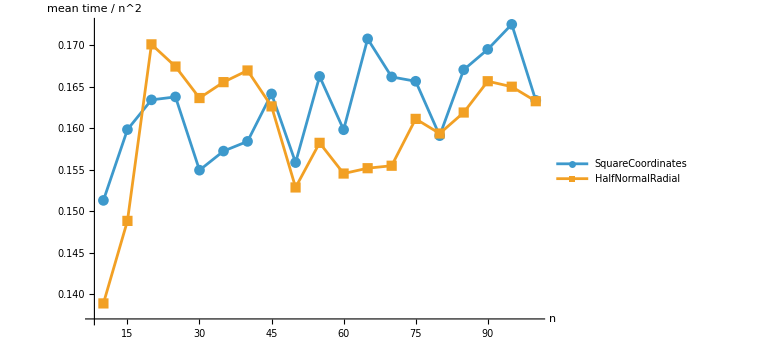

```mathematica
ListLinePlot[
  Values[scaledDataByEnsemble],
  PlotMarkers -> Automatic,
  PlotLegends -> Keys[scaledDataByEnsemble],
  AxesLabel -> {
    "n",
    "mean time / n^2"
  },
  PlotRange -> All,
  ImageSize -> Large
]

fitEnsemble[summary_List, ensemble_String] := Module[
  {data, fit},

  data = Cases[
    summary,
    row_ /;
      row["ensemble"] == ensemble &&
      NumericQ[row["meanTime"]] :>
      {
        row["n"],
        row["meanTime"]
      }
  ];

  fit = LinearModelFit[
    data,
    {1, n, n^2},
    n
  ];

  <|
    "ensemble" -> ensemble,
    "fit" -> fit,
    "parameters" ->
      fit["BestFitParameters"],
    "adjustedRSquared" ->
      fit["AdjustedRSquared"],
    "data" -> data
  |>
];

squareFit =
  fitEnsemble[
    comparisonSummary,
    "SquareCoordinates"
  ];

halfNormalFit =
  fitEnsemble[
    comparisonSummary,
    "HalfNormalRadial"
  ];
```

```mathematica
Dataset[{
<|
"ensemble"->squareFit["ensemble"],
"parameters"->squareFit["parameters"],"adjustedRSquared"->squareFit["adjustedRSquared"]
|>,
<|
"ensemble"->halfNormalFit["ensemble"],
"parameters"->halfNormalFit["parameters"],"adjustedRSquared"->halfNormalFit["adjustedRSquared"]
|>
}]

powerLawFit[summary_List,ensemble_String]:=Module[{data,fit},data=Cases[summary,row_/;row["ensemble"]==ensemble&&NumericQ[row["meanTime"]]&&row["meanTime"]>0:>{Log[row["n"]],Log[row["meanTime"]]}];
fit=LinearModelFit[data,x,x];
<|"ensemble"->ensemble,"logIntercept"->fit["BestFitParameters"][[1]],"exponent"->fit["BestFitParameters"][[2]],"prefactor"->Exp[fit["BestFitParameters"][[1]]],"adjustedRSquared"->fit["AdjustedRSquared"]|>];

powerLawResults={
powerLawFit[
comparisonSummary,
"SquareCoordinates"
],
powerLawFit[
comparisonSummary,
"HalfNormalRadial"
]};

Dataset[powerLawResults]
```

## 10. Regression residuals

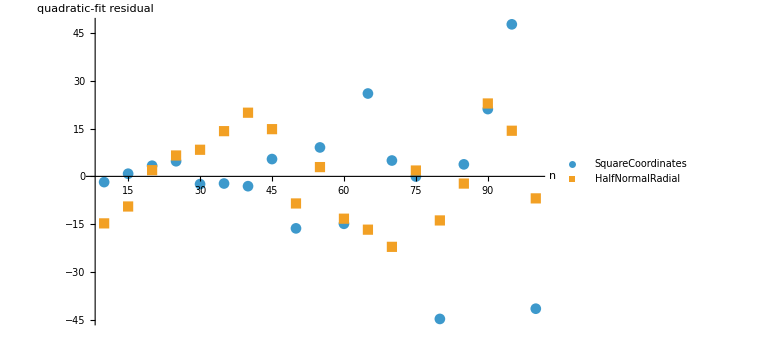

```mathematica
squareResidualData=If[
Head[squareQuadraticFit]===FittedModel,Table[
{point[[1]],
point[[2]]-squareQuadraticFit[point[[1]]]
},
{point,squareMeanTimeData}
],
{}
];

halfNormalResidualData=If[
Head[halfNormalQuadraticFit]===FittedModel,
Table[
{
point[[1]],
point[[2]]-halfNormalQuadraticFit[point[[1]]]
},
{point,halfNormalMeanTimeData}
],
{}
];

residualSummary=Dataset@{
<|
"ensemble"->"SquareCoordinates",
"residualCount"->Length[squareResidualData],
"meanResidual"->If[
Length[squareResidualData]>0,
Mean[squareResidualData[[All,2]]],
Missing["InsufficientData"]
],
"rootMeanSquareResidual"->If[
Length[squareResidualData]>0,
Sqrt[Mean[squareResidualData[[All,2]]^2]],
Missing["InsufficientData"]
],
"maximumAbsoluteResidual"->If[
Length[squareResidualData]>0,
Max[Abs[squareResidualData[[All,2]]]],
Missing["InsufficientData"]
]
|>,
<|
"ensemble"->"HalfNormalRadial",
"residualCount"->Length[halfNormalResidualData],
"meanResidual"->If[
Length[halfNormalResidualData]>0,
Mean[halfNormalResidualData[[All,2]]],
Missing["InsufficientData"]
],
"rootMeanSquareResidual"->If[
Length[halfNormalResidualData]>0,
Sqrt[Mean[halfNormalResidualData[[All,2]]^2]],
Missing["InsufficientData"]
],
"maximumAbsoluteResidual"->If[
Length[halfNormalResidualData]>0,
Max[Abs[halfNormalResidualData[[All,2]]]],
Missing["InsufficientData"]
]
|>
};

residualSummary

If[
Length[squareResidualData]>0||
Length[halfNormalResidualData]>0,
ListPlot[
{
squareResidualData,
halfNormalResidualData
},
PlotMarkers->Automatic,
PlotLegends->{
"SquareCoordinates",
"HalfNormalRadial"
},
AxesLabel->{
"n",
"quadratic-fit residual"
},
PlotRange->All,
GridLines->{
None,
{0}
},
ImageSize->Large
],
Missing["InsufficientData"]
]
```

## 11. Confidence bands for retained means

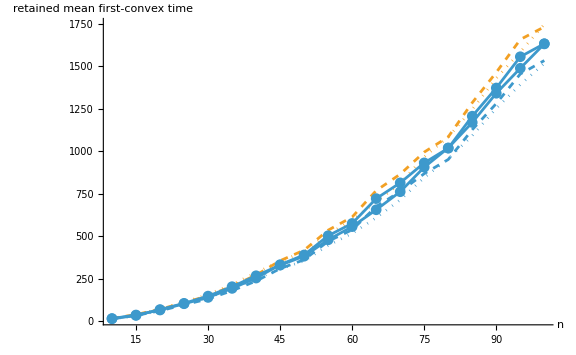

```mathematica
confidenceDataByEnsemble=GroupBy[
Cases[
comparisonSummary,row_/;
NumericQ[row["meanTime"]]&&
NumericQ[row["standardError"]]:>
{
row["ensemble"],
row["n"],
row["meanTime"],
row["meanTime"]-1.96 row["standardError"],row["meanTime"]+1.96 row["standardError"]
}
],
First->Rest
];

squareConfidenceData=Lookup[
confidenceDataByEnsemble,
"SquareCoordinates",
{}
];

halfNormalConfidenceData=Lookup[
confidenceDataByEnsemble,
"HalfNormalRadial",
{}
];

confidenceSummary=Dataset@{
<|
"ensemble"->"SquareCoordinates",
"dataPoints"->Length[squareConfidenceData],
"minimumLowerBound"->If[
Length[squareConfidenceData]>0,
Min[squareConfidenceData[[All,3]]],
Missing["InsufficientData"]
],
"maximumUpperBound"->If[
Length[squareConfidenceData]>0,
Max[squareConfidenceData[[All,4]]],
Missing["InsufficientData"]
]
|>,
<|
"ensemble"->"HalfNormalRadial",
"dataPoints"->Length[halfNormalConfidenceData],
"minimumLowerBound"->If[
Length[halfNormalConfidenceData]>0,
Min[halfNormalConfidenceData[[All,3]]],
Missing["InsufficientData"]
],
"maximumUpperBound"->If[
Length[halfNormalConfidenceData]>0,
Max[halfNormalConfidenceData[[All,4]]],
Missing["InsufficientData"]
]
|>
};

confidenceSummary

If[
Length[squareConfidenceData]>0||
Length[halfNormalConfidenceData]>0,
Show[
{
If[Length[squareConfidenceData]>0,
ListLinePlot[
{squareConfidenceData[[All,{1,3}]],
squareConfidenceData[[All,{1,4}]]
},
PlotStyle->{
Directive[Dashed],
Directive[Dashed]
}
],
Nothing
],
If[
Length[halfNormalConfidenceData]>0,
ListLinePlot[
{
halfNormalConfidenceData[[All,{1,3}]],
halfNormalConfidenceData[[All,{1,4}]]
},
PlotStyle->{
Directive[Dotted],
Directive[Dotted]
}
],
Nothing
],
If[
Length[squareConfidenceData]>0,
ListPlot[
squareConfidenceData[[All,{1,2}]],
Joined->True,
PlotMarkers->Automatic
],
Nothing
],
If[
Length[halfNormalConfidenceData]>0,
ListPlot[
halfNormalConfidenceData[[All,{1,2}]],
Joined->True,
PlotMarkers->Automatic
],
Nothing
]
},
AxesLabel->{
"n",
"retained mean first-convex time"
},
PlotRange->All,
PlotLegends->{
"Square lower 95%",
"Square upper 95%",
"Half-normal lower 95%",
"Half-normal upper 95%",
"Square mean",
"Half-normal mean"
},
ImageSize->Large
],
Missing["InsufficientData"]
]
```

## 12. Spectral-gap prediction

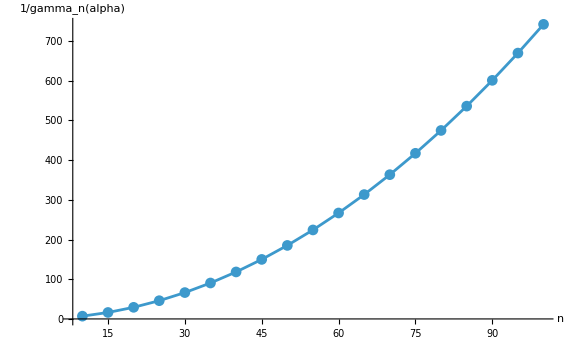

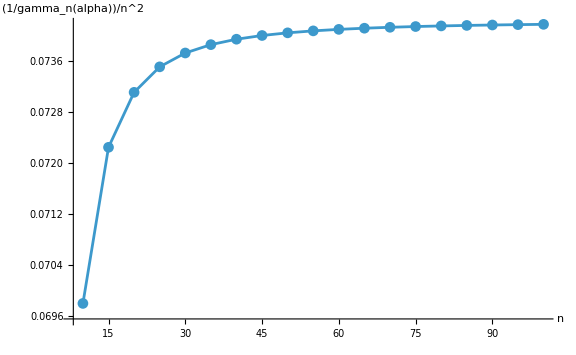

```mathematica
muSquared[
n_Integer?Positive,
k_Integer,
alpha_?NumericQ
]:=
1-2 alpha (1-alpha) (1-Cos[2 Pi k/n]);

gamma[
n_Integer?Positive,
alpha_?NumericQ
]:=
1/2 Log[
muSquared[n,1,alpha]/
muSquared[n,2,alpha]
];

spectralTimeScale[
n_Integer?Positive,
alpha_?NumericQ
]:=
1/gamma[n,alpha];

spectralScaleData=Table[
{
n,
spectralTimeScale[n,alphaComparison]
},
{n,nValuesComparison}
];

spectralScaleSummary=Dataset@{
<|
"alpha"->alphaComparison,
"minimumN"->Min[nValuesComparison],
"maximumN"->Max[nValuesComparison],"minimumSpectralScale"->Min[spectralScaleData[[All,2]]],"maximumSpectralScale"->Max[spectralScaleData[[All,2]]]
|>
};

spectralScaleSummary

ListLinePlot[
spectralScaleData,
PlotMarkers->Automatic,
AxesLabel->{
"n",
"1/gamma_n(alpha)"
},
PlotRange->All,
ImageSize->Large
]

scaledSpectralData=Table[
{
n,
spectralTimeScale[n,alphaComparison]/n^2
},
{n,nValuesComparison}
];

ListLinePlot[
scaledSpectralData,
PlotMarkers->Automatic,
AxesLabel->{
"n",
"(1/gamma_n(alpha))/n^2"
},
PlotRange->All,
ImageSize->Large
]
```

## 13. Calibrated spectral prediction

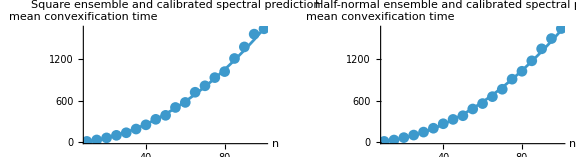

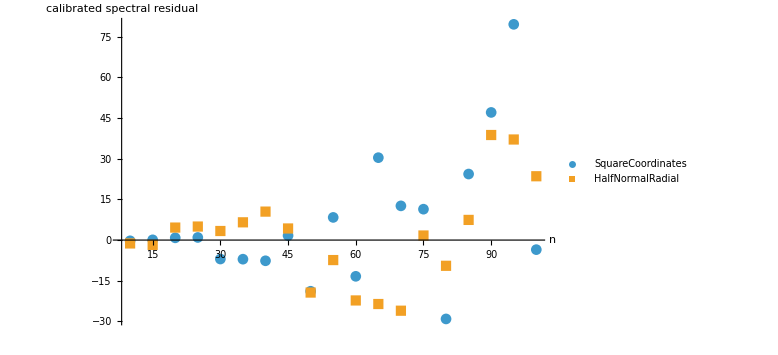

```mathematica
calibrateSpectralScale[
meanData_List,
alpha_?NumericQ
]:=If[
Length[meanData]>0,
Mean@Table[
point[[2]]/
spectralTimeScale[point[[1]],alpha],
{point,meanData}
],
Missing["InsufficientData"]
];

squareSpectralCalibration=calibrateSpectralScale[
squareMeanTimeData,
alphaComparison
];

halfNormalSpectralCalibration=calibrateSpectralScale[
halfNormalMeanTimeData,
alphaComparison
];

squareSpectralPrediction=If[
NumericQ[squareSpectralCalibration],Table[
{
n,
squareSpectralCalibration*
spectralTimeScale[n,alphaComparison]
},
{n,nValuesComparison}
],
{}
];

halfNormalSpectralPrediction=If[NumericQ[halfNormalSpectralCalibration],
Table[
{
n,
halfNormalSpectralCalibration*
spectralTimeScale[n,alphaComparison]
},
{n,nValuesComparison}
],
{}
];

squareSpectralResiduals=If[
NumericQ[squareSpectralCalibration],
Table[{
point[[1]],
point[[2]]-squareSpectralCalibration*
spectralTimeScale[
point[[1]],
alphaComparison
]
},
{point,squareMeanTimeData}
],
{}
];

halfNormalSpectralResiduals=If[
NumericQ[halfNormalSpectralCalibration],
Table[{
point[[1]],
point[[2]]-halfNormalSpectralCalibration*
spectralTimeScale[
point[[1]],
alphaComparison
]
},
{point,halfNormalMeanTimeData}
],
{}
];

calibratedSpectralSummary=Dataset@{
<|
"ensemble"->"SquareCoordinates",
"calibration"->squareSpectralCalibration,
"rootMeanSquareResidual"->If[
Length[squareSpectralResiduals]>0,
Sqrt[
Mean[
squareSpectralResiduals[[All,2]]^2
]
],
Missing["InsufficientData"]
],
"maximumAbsoluteResidual"->If[
Length[squareSpectralResiduals]>0,
Max[
Abs[
squareSpectralResiduals[[All,2]]
]
],
Missing["InsufficientData"]
]
|>,
<|
"ensemble"->"HalfNormalRadial",
"calibration"->halfNormalSpectralCalibration,"rootMeanSquareResidual"->If[
Length[halfNormalSpectralResiduals]>0,Sqrt[
Mean[
halfNormalSpectralResiduals[[All,2]]^2
]
],
Missing["InsufficientData"]
],
"maximumAbsoluteResidual"->If[
Length[halfNormalSpectralResiduals]>0,Max[
Abs[
halfNormalSpectralResiduals[[All,2]]
]
],
Missing["InsufficientData"]
]
|>
};

calibratedSpectralSummary

GraphicsRow[
{
If[
Length[squareSpectralPrediction]>0,
Show[
ListPlot[
squareMeanTimeData,
PlotMarkers->Automatic
],
ListLinePlot[
squareSpectralPrediction
],
AxesLabel->{
"n",
"mean convexification time"
},
PlotRange->All,
PlotLabel->"Square ensemble and calibrated spectral prediction",ImageSize->Large
],
Missing["InsufficientData"]
],
If[
Length[
halfNormalSpectralPrediction]>0,
Show[
ListPlot[
halfNormalMeanTimeData,
PlotMarkers->Automatic
],
ListLinePlot[
halfNormalSpectralPrediction
],
AxesLabel->{
"n",
"mean convexification time"
},
PlotRange->All,PlotLabel->"Half-normal ensemble and calibrated spectral prediction",ImageSize->Large
],
Missing["InsufficientData"]
]
},
ImageSize->Large
]

If[
Length[squareSpectralResiduals]>0||
Length[halfNormalSpectralResiduals]>0,
ListPlot[
{
squareSpectralResiduals,
halfNormalSpectralResiduals
},
PlotMarkers->Automatic,
PlotLegends->{
"SquareCoordinates",
"HalfNormalRadial"
},
AxesLabel->{
"n",
"calibrated spectral residual"
},
GridLines->{
None,
{0}
},
PlotRange->All,
ImageSize->Large
],
Missing["InsufficientData"]
]
```

## 14. Dependence on alpha

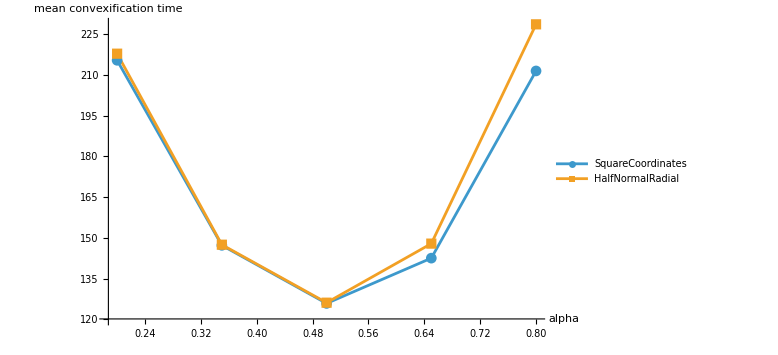

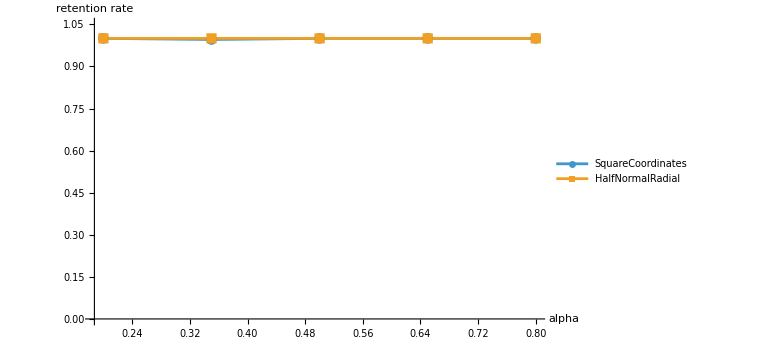

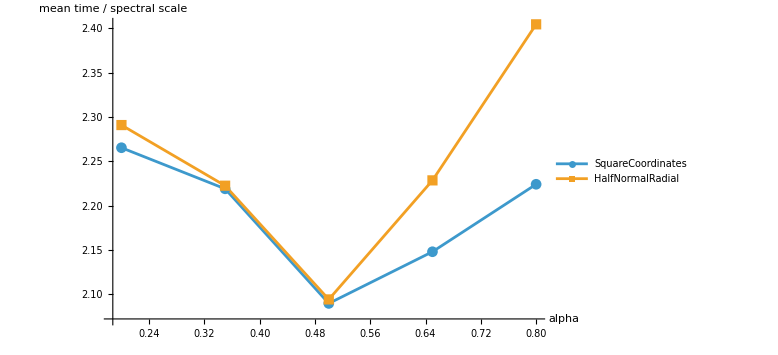

```mathematica
alphaValues={0.2,0.35,0.5,0.65,0.8};

alphaComparisonN=30;
alphaTrials=250;
alphaMaxM=7500;
alphaSeedBase=90000;

alphaEnsembleData=Flatten@Table[
Join[
runConvexificationExperiment[
randomCenteredPolygon,
"SquareCoordinates",
{alphaComparisonN},
alpha,
alphaTrials,
alphaMaxM,
alphaSeedBase+Round[1000 alpha]
],
runConvexificationExperiment[
randomHalfNormalPolygon,
"HalfNormalRadial",
{alphaComparisonN},
alpha,
alphaTrials,
alphaMaxM,
alphaSeedBase+Round[1000 alpha]
]
],
{alpha,alphaValues}
];

summarizeByEnsembleAndAlpha[data_List]:=Module[
{groups},

groups=GroupBy[
data,
{#ensemble,#alpha}&
];

KeyValueMap[
Function[{key,rows},
Module[
{
times,
retainedCount,
totalCount
},

times=Cases[
rows[[All,"time"]],
_Integer
];

retainedCount=Length[times];
totalCount=Length[rows];

<|
"ensemble"->key[[1]],
"alpha"->key[[2]],
"n"->alphaComparisonN,
"trials"->totalCount,
"retained"->retainedCount,
"retentionRate"->
N[retainedCount/totalCount],
"meanTime"->If[
retainedCount>0,
Mean[times],
Missing["NoRetainedTrials"]
],
"medianTime"->If[
retainedCount>0,
Median[times],
Missing["NoRetainedTrials"]
],
"standardDeviation"->If[
retainedCount>1,
StandardDeviation[times],
Missing["InsufficientData"]
],
"standardError"->If[
retainedCount>1,
StandardDeviation[times]/
Sqrt[retainedCount],
Missing["InsufficientData"]
],
"spectralScale"->
spectralTimeScale[
alphaComparisonN,
key[[2]]
]
|>
]
],
groups
]
];

alphaSummary=
summarizeByEnsembleAndAlpha[
alphaEnsembleData
];

Dataset[alphaSummary]

alphaMeanDataByEnsemble=GroupBy[
Cases[
alphaSummary,
row_/;NumericQ[row["meanTime"]]:>
{
row["ensemble"],
row["alpha"],
row["meanTime"]
}
],
First->Rest
];

squareAlphaMeanData=Lookup[
alphaMeanDataByEnsemble,
"SquareCoordinates",
{}
];

halfNormalAlphaMeanData=Lookup[
alphaMeanDataByEnsemble,
"HalfNormalRadial",
{}
];

If[
Length[squareAlphaMeanData]>0||
Length[halfNormalAlphaMeanData]>0,

ListLinePlot[
{
squareAlphaMeanData,
halfNormalAlphaMeanData
},
PlotMarkers->Automatic,
PlotLegends->{
"SquareCoordinates",
"HalfNormalRadial"
},
AxesLabel->{
"alpha",
"mean convexification time"
},
PlotRange->All,
ImageSize->Large
],

Missing["InsufficientData"]
]

alphaRetentionDataByEnsemble=GroupBy[
Cases[
alphaSummary,
row_/;NumericQ[row["retentionRate"]]:>
{
row["ensemble"],
row["alpha"],
row["retentionRate"]
}
],
First->Rest
];

squareAlphaRetentionData=Lookup[
alphaRetentionDataByEnsemble,
"SquareCoordinates",
{}
];

halfNormalAlphaRetentionData=Lookup[
alphaRetentionDataByEnsemble,
"HalfNormalRadial",
{}
];

If[
Length[squareAlphaRetentionData]>0||
Length[halfNormalAlphaRetentionData]>0,

ListLinePlot[
{
squareAlphaRetentionData,
halfNormalAlphaRetentionData
},
PlotMarkers->Automatic,
PlotLegends->{
"SquareCoordinates",
"HalfNormalRadial"
},
AxesLabel->{
"alpha",
"retention rate"
},
PlotRange->{0,1.05},
ImageSize->Large],
Missing["InsufficientData"]
]

alphaNormalizedMeanDataByEnsemble=GroupBy[
Cases[
alphaSummary,
row_/;
NumericQ[row["meanTime"]]&&
NumericQ[row["spectralScale"]]:>
{
row["ensemble"],
row["alpha"],
row["meanTime"]/
row["spectralScale"]
}
],
First->Rest
];

squareAlphaNormalizedMeanData=Lookup[
alphaNormalizedMeanDataByEnsemble,
"SquareCoordinates",
{}
];

halfNormalAlphaNormalizedMeanData=Lookup[
alphaNormalizedMeanDataByEnsemble,
"HalfNormalRadial",
{}
];

If[
Length[squareAlphaNormalizedMeanData]>0||Length[halfNormalAlphaNormalizedMeanData]>0,

ListLinePlot[
{
squareAlphaNormalizedMeanData,
halfNormalAlphaNormalizedMeanData
},
PlotMarkers->Automatic,
PlotLegends->{
"SquareCoordinates",
"HalfNormalRadial"
},
AxesLabel->{
"alpha",
"mean time / spectral scale"
},
PlotRange->All,
ImageSize->Large
],

Missing["InsufficientData"]
]
```

## 15. Symmetry under alpha -> 1 - alpha

-Graphics-

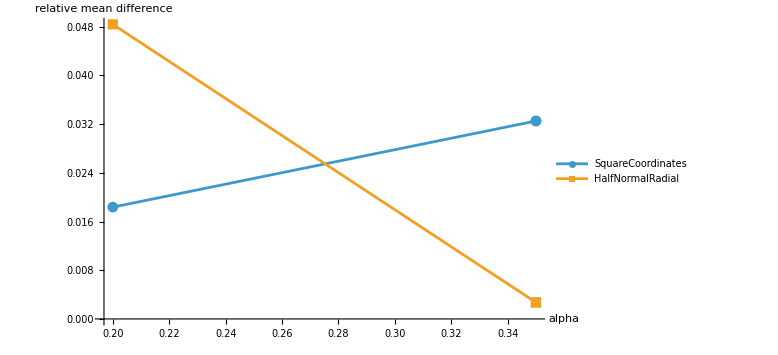

```mathematica
alphaSymmetryPairs={
{0.2,0.8},
{0.35,0.65}
};

alphaSummaryRow[
summary_List,
ensemble_String,
alpha_?NumericQ
]:=
SelectFirst[
summary,
#ensemble==ensemble&&
Abs[#alpha-alpha]<10^-12&,
Missing[
"NotFound",
<|
"ensemble"->ensemble,
"alpha"->alpha
|>
]
];

alphaSymmetryComparison[
summary_List,
ensemble_String
]:=Table[
Module[
{
alpha,
oneMinusAlpha,
left,
right,
leftMean,
rightMean,
leftMedian,
rightMedian,
leftRetention,
rightRetention,
leftScale,
rightScale
},

alpha=pair[[1]];
oneMinusAlpha=pair[[2]];

left=alphaSummaryRow[
summary,
ensemble,
alpha
];

right=alphaSummaryRow[
summary,
ensemble,
oneMinusAlpha
];

leftMean=If[
AssociationQ[left],
left["meanTime"],
Missing["Unavailable"]
];

rightMean=If[
AssociationQ[right],
right["meanTime"],
Missing["Unavailable"]
];

leftMedian=If[
AssociationQ[left],
left["medianTime"],
Missing["Unavailable"]
];

rightMedian=If[
AssociationQ[right],
right["medianTime"],
Missing["Unavailable"]
];

leftRetention=If[
AssociationQ[left],
left["retentionRate"],
Missing["Unavailable"]
];

rightRetention=If[
AssociationQ[right],
right["retentionRate"],
Missing["Unavailable"]
];

leftScale=If[
AssociationQ[left],
left["spectralScale"],
Missing["Unavailable"]
];

rightScale=If[
AssociationQ[right],
right["spectralScale"],
Missing["Unavailable"]
];

<|
"ensemble"->ensemble,
"alpha"->alpha,
"oneMinusAlpha"->oneMinusAlpha,
"meanAtAlpha"->leftMean,
"meanAtOneMinusAlpha"->rightMean,
"meanAbsoluteDifference"->If[
NumericQ[leftMean]&&
NumericQ[rightMean],
Abs[leftMean-rightMean],
Missing["Unavailable"]
],

"meanRelativeDifference"->If[
NumericQ[leftMean]&&
NumericQ[rightMean]&&
Mean[{leftMean,rightMean}]!=0,
Abs[leftMean-rightMean]/
Mean[{leftMean,rightMean}],
Missing["Unavailable"]
],

"medianAtAlpha"->leftMedian,
"medianAtOneMinusAlpha"->rightMedian,
"medianAbsoluteDifference"->If[
NumericQ[leftMedian]&&NumericQ[rightMedian],
Abs[leftMedian-rightMedian],
Missing["Unavailable"]
],

"retentionAtAlpha"->leftRetention,
"retentionAtOneMinusAlpha"->rightRetention,
"retentionAbsoluteDifference"->If[
NumericQ[leftRetention]&&
NumericQ[rightRetention],
Abs[
leftRetention-
rightRetention
],
Missing["Unavailable"]
],

"spectralScaleAtAlpha"->leftScale,
"spectralScaleAtOneMinusAlpha"->
rightScale,
"spectralScaleAbsoluteDifference"->If[
NumericQ[leftScale]&&
NumericQ[rightScale],
Abs[leftScale-rightScale],
Missing["Unavailable"]
]
|>
],
{pair,alphaSymmetryPairs}
];

squareAlphaSymmetry=
alphaSymmetryComparison[
alphaSummary,
"SquareCoordinates"
];

halfNormalAlphaSymmetry=
alphaSymmetryComparison[
alphaSummary,
"HalfNormalRadial"
];

alphaSymmetrySummary=Dataset@Join[
squareAlphaSymmetry,
halfNormalAlphaSymmetry
];

alphaSymmetrySummary

squareAlphaSymmetryPlotData=Cases[
squareAlphaSymmetry,
row_/;
NumericQ[row["meanAtAlpha"]]&&
NumericQ[
row["meanAtOneMinusAlpha"]
]:>
{
row["alpha"],
row["meanAtAlpha"],
row["meanAtOneMinusAlpha"]
}
];

halfNormalAlphaSymmetryPlotData=Cases[
halfNormalAlphaSymmetry,
row_/;
NumericQ[row["meanAtAlpha"]]&&
NumericQ[
row["meanAtOneMinusAlpha"]
]:>
{
row["alpha"],
row["meanAtAlpha"],
row["meanAtOneMinusAlpha"]
}
];

GraphicsRow[
{
If[
Length[
squareAlphaSymmetryPlotData
]>0,
ListPlot[
{
squareAlphaSymmetryPlotData[[
All,{1,2}
]],
squareAlphaSymmetryPlotData[[
All,{1,3}
]]
},
Joined->True,
PlotMarkers->Automatic,
PlotLegends->{
"mean at alpha",
"mean at 1 - alpha"
},
AxesLabel->{
"alpha",
"mean convexification time"
},
PlotLabel->
"Square-coordinate ensemble",
PlotRange->All,
ImageSize->Large
],
Missing["InsufficientData"]
],

If[
Length[
halfNormalAlphaSymmetryPlotData
]>0,
ListPlot[
{
halfNormalAlphaSymmetryPlotData[[
All,{1,2}
]],
halfNormalAlphaSymmetryPlotData[[
All,{1,3}
]]},
Joined->True,
PlotMarkers->Automatic,
PlotLegends->{
"mean at alpha",
"mean at 1 - alpha"
},
AxesLabel->{
"alpha",
"mean convexification time"
},
PlotLabel->
"Half-normal radial ensemble",
PlotRange->All,
ImageSize->Large
],
Missing["InsufficientData"]
]
},
ImageSize->Large
]

alphaSymmetryDifferenceDataByEnsemble=
GroupBy[
Cases[
Join[
squareAlphaSymmetry,
halfNormalAlphaSymmetry
],
row_/;
NumericQ[
row["meanRelativeDifference"]
]:>
{
row["ensemble"],
row["alpha"],
row["meanRelativeDifference"]
}
],
First->Rest
];

If[
Length[
alphaSymmetryDifferenceDataByEnsemble
]>0,
ListPlot[
Values[
alphaSymmetryDifferenceDataByEnsemble
],
Joined->True,
PlotMarkers->Automatic,
PlotLegends->Keys[
alphaSymmetryDifferenceDataByEnsemble
],
AxesLabel->{
"alpha",
"relative mean difference"
},
PlotRange->All,
ImageSize->Large
],
Missing["InsufficientData"]
]
```

## 16. Retention-rate diagnostics

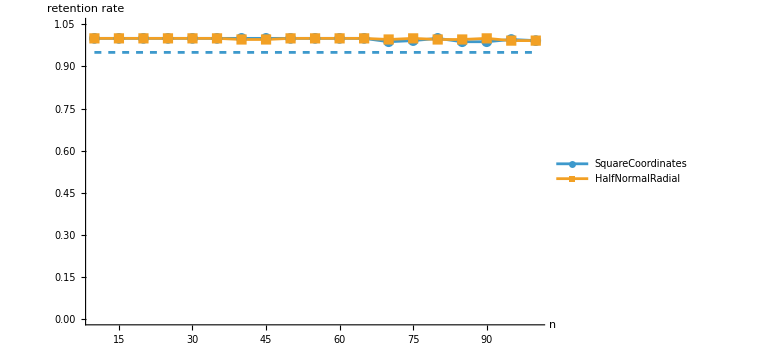

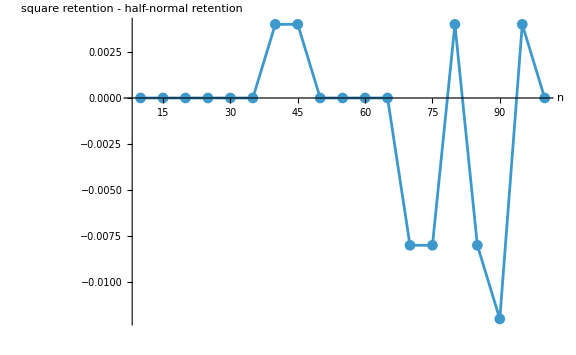

```mathematica
retentionDataByEnsemble=GroupBy[
Cases[
comparisonSummary,
row_/;NumericQ[row["retentionRate"]]:>
{
row["ensemble"],
row["n"],
row["retentionRate"]
}
],
First->Rest
];

squareRetentionData=Lookup[
retentionDataByEnsemble,
"SquareCoordinates",
{}
];

halfNormalRetentionData=Lookup[
retentionDataByEnsemble,
"HalfNormalRadial",
{}
];

retentionThreshold=0.95;

lowRetentionRows=Select[
comparisonSummary,
NumericQ[#retentionRate]&&
#retentionRate<retentionThreshold&
];

retentionSummary=Dataset@{
<|
"ensemble"->"SquareCoordinates",
"dataPoints"->Length[squareRetentionData],"minimumRetentionRate"->If[
Length[squareRetentionData]>0,
Min[squareRetentionData[[All,2]]],
Missing["InsufficientData"]
],
"meanRetentionRate"->If[
Length[squareRetentionData]>0,
Mean[squareRetentionData[[All,2]]],
Missing["InsufficientData"]
],

"groupsBelowThreshold"->Count[
squareRetentionData,
{_,rate_}/;rate<retentionThreshold
]
|>,
<|
"ensemble"->"HalfNormalRadial",
"dataPoints"->Length[halfNormalRetentionData],"minimumRetentionRate"->If[
Length[halfNormalRetentionData]>0,
Min[halfNormalRetentionData[[All,2]]],
Missing["InsufficientData"]
],
"meanRetentionRate"->If[
Length[halfNormalRetentionData]>0,
Mean[halfNormalRetentionData[[All,2]]],
Missing["InsufficientData"]
],
"groupsBelowThreshold"->Count[
halfNormalRetentionData,{_,rate_}/;rate<retentionThreshold
]
|>
};

retentionSummary

If[
Length[
squareRetentionData]>0||
Length[halfNormalRetentionData]>0,

Show[
ListLinePlot[
{
squareRetentionData,
halfNormalRetentionData
},
PlotMarkers->Automatic,
PlotLegends->{"SquareCoordinates","HalfNormalRadial"}
],
Plot[
retentionThreshold,
{
n,
Min[nValuesComparison],
Max[nValuesComparison]
},
PlotStyle->Dashed
],
AxesLabel->{
"n",
"retention rate"
},
PlotRange->{
{
Min[nValuesComparison],
Max[nValuesComparison]
},
{0,1.05}
},
ImageSize->Large
],

Missing["InsufficientData"]
]

If[
Length[lowRetentionRows]>0,Dataset[Map[
<|
"ensemble"->#["ensemble"],
"n"->#["n"],
"trials"->#["trials"],
"retained"->#["retained"],
"retentionRate"->#["retentionRate"],
"maximumIterations"->
maxMComparison
|>&,
lowRetentionRows
]
],Dataset@{
<|
"status"->
"All ensemble-by-n groups meet the retention threshold.",
"threshold"->retentionThreshold,
"maximumIterations"->
maxMComparison
|>
}
]

retentionDifferenceData=Module[
{
squareAssociation,
halfNormalAssociation,
commonN
},

squareAssociation=Association[
Rule@@@squareRetentionData
];

halfNormalAssociation=Association[
Rule@@@halfNormalRetentionData
];

commonN=Intersection[
Keys[squareAssociation],
Keys[halfNormalAssociation]
];

Table[
{
n,
squareAssociation[n]-
halfNormalAssociation[n]
},
{n,commonN}
]
];

If[
Length[retentionDifferenceData]>0,

ListPlot[
retentionDifferenceData,
Joined->True,
PlotMarkers->Automatic,
AxesLabel->{
"n",
"square retention - half-normal retention"
},
GridLines->{
None,
{0}
},
PlotRange->All,
ImageSize->Large
],

Missing["InsufficientData"]
]
```

## 17. Reproducible larger experiment

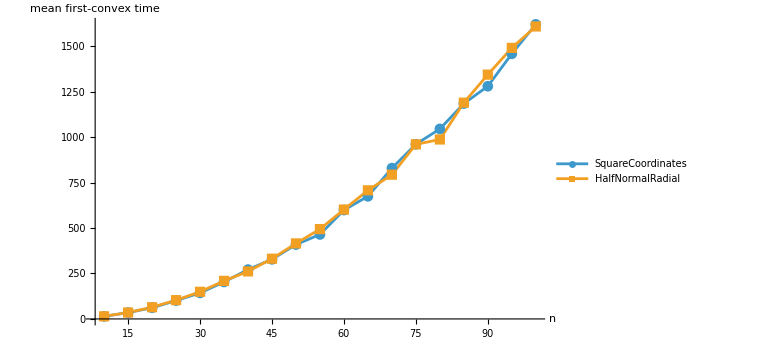

```mathematica
Clear[runLargerExperiment];

largerExperimentParameters=<|
"nValues"->Range[10,100,5],
"Alpha"->alphaComparison,
"Trials"->250,
"MaxIterations"->maxMComparison,
"SeedBase"->140000
|>;

runLargerExperiment[]:=
runLargerExperiment[largerExperimentParameters];

runLargerExperiment[
parameters_Association
]:=Module[
{
nValues,
alpha,
trials,
maxIterations,
seedBase,
squareData,
halfNormalData,
combinedData,
summary
},

nValues=Lookup[
parameters,
"nValues",
Range[10,100,5]
];

alpha=Lookup[
parameters,
"Alpha",
0.35
];

trials=Lookup[
parameters,
"Trials",
250
];

maxIterations=Lookup[
parameters,
"MaxIterations",
7500
];

seedBase=Lookup[
parameters,
"SeedBase",
140000
];

squareData=runConvexificationExperiment[
randomCenteredPolygon,
"SquareCoordinates",
nValues,
alpha,
trials,
maxIterations,
seedBase
];

halfNormalData=runConvexificationExperiment[
randomHalfNormalPolygon,
"HalfNormalRadial",
nValues,
alpha,
trials,
maxIterations,
seedBase
];

combinedData=Join[
squareData,
halfNormalData
];

summary=
summarizeByEnsembleAndN[
combinedData
];

<|
"Parameters"->parameters,
"TrialData"->combinedData,
"Summary"->summary
|>
];

largerExperiment=runLargerExperiment[];

largerExperimentParameterSummary=Dataset@{
<|
"parameter"->"n values",
"value"->
largerExperimentParameters["nValues"]
|>,
<|
"parameter"->"alpha",
"value"->
largerExperimentParameters["Alpha"]
|>,
<|
"parameter"->
"trials per n and ensemble",
"value"->
largerExperimentParameters["Trials"]
|>,
<|
"parameter"->"maximum iterations",
"value"->
largerExperimentParameters["MaxIterations"]
|>,
<|
"parameter"->"seed base",
"value"->
largerExperimentParameters["SeedBase"]
|>,
<|
"parameter"->"total trials","value"->
2*
Length[
largerExperimentParameters[
"nValues"
]
]*
largerExperimentParameters[
"Trials"
]
|>
};

largerExperimentParameterSummary

largerExperimentSummary=
largerExperiment["Summary"];

Dataset[
largerExperimentSummary
]

largerExperimentRetentionCheck=Select[
largerExperimentSummary,
NumericQ[#retentionRate]&&
#retentionRate<retentionThreshold&
];

If[
Length[
largerExperimentRetentionCheck
]>0,

Dataset[
largerExperimentRetentionCheck
],

Dataset@{
<|
"status"->
"All groups meet the retention threshold.",
"threshold"->
retentionThreshold,
"maximumIterations"->
largerExperimentParameters[
"MaxIterations"
]
|>
}
]

largerMeanDataByEnsemble=GroupBy[
Cases[
largerExperimentSummary,
row_/;
NumericQ[row["meanTime"]]:>
{
row["ensemble"],
row["n"],
row["meanTime"]
}
],
First->Rest
];

largerSquareMeanData=Lookup[
largerMeanDataByEnsemble,
"SquareCoordinates",
{}
];

largerHalfNormalMeanData=Lookup[
largerMeanDataByEnsemble,
"HalfNormalRadial",
{}
];

If[
Length[largerSquareMeanData]>0||
Length[largerHalfNormalMeanData]>0,

ListLinePlot[
{
largerSquareMeanData,
largerHalfNormalMeanData
},
PlotMarkers->Automatic,
PlotLegends->{
"SquareCoordinates",
"HalfNormalRadial"
},
AxesLabel->{
"n",
"mean first-convex time"
},
PlotRange->All,
ImageSize->Large
],

Missing["InsufficientData"]
]
```

## 18. Automated verification report

```mathematica
Clear[
verificationReport,
verificationIteratePhysical,
firstStrictConvexTimeByPolygonAtTime
];

verificationIteratePhysical[
p_List,
alpha_?NumericQ,
m_Integer?NonNegative
]:=Nest[
applyA[#,alpha]&,
N[p],
m
];

firstStrictConvexTimeByPolygonAtTime[
p_List,
alpha_?NumericQ,
maxIterations_Integer?NonNegative,
tol_?NumericQ
]:=SelectFirst[
Range[0,maxIterations],
TrueQ[
strictlyConvexQ[
polygonAtTime[p,alpha,#],
tol
]
]&,
Missing["NotFound",maxIterations]
];

verificationReport[]:=
verificationReport[
Range[8,24,2],
0.35,
1500,
10^-10
];

verificationReport[
nValues_List,
alpha_?NumericQ,
maxIterations_Integer?NonNegative
]:=
verificationReport[
nValues,
alpha,
maxIterations,
10^-10
];

verificationReport[
nValues_List,
alpha_?NumericQ,
maxIterations_Integer?NonNegative,
tol_?NumericQ
]:=Module[
{rows},

rows=Table[
Module[
{
squarePolygon,
halfNormalPolygon,

squareTime,
halfNormalTime,

squareIndependentTime,
halfNormalIndependentTime,

squareCentered,
halfNormalCentered,

squareOneStepError,
halfNormalOneStepError,

squareIterateError,
halfNormalIterateError,

squareConvexAtTime,
halfNormalConvexAtTime,

squareNotConvexEarlier,
halfNormalNotConvexEarlier,

squareFirstHitAgreement,
halfNormalFirstHitAgreement,

gapValue
},

squarePolygon=
randomCenteredPolygon[
n,
210000+n
];

halfNormalPolygon=
randomHalfNormalPolygon[
n,
220000+n
];

squareCentered=
TrueQ[
Abs[
Mean[squarePolygon]]<
tol
];

halfNormalCentered=
TrueQ[
Abs[
Mean[halfNormalPolygon]]<
tol
];

squareOneStepError=
Norm[
applyA[
squarePolygon,
alpha]-
polygonAtTime[
squarePolygon,
alpha,
1
]
];

halfNormalOneStepError=
Norm[
applyA[
halfNormalPolygon,alpha
]-
polygonAtTime[
halfNormalPolygon,
alpha,
1
]
];

squareIterateError=
Max@Table[
Norm[
verificationIteratePhysical[
squarePolygon,
alpha,
m
]-
polygonAtTime[
squarePolygon,
alpha,
m
]
],
{m,0,12}
];

halfNormalIterateError=
Max@Table[
Norm[
verificationIteratePhysical[
halfNormalPolygon,
alpha,
m
]-
polygonAtTime[
halfNormalPolygon,
alpha,
m
]
],
{m,0,12}
];

squareTime=
firstStrictConvexTime[
squarePolygon,
alpha,
maxIterations,
tol
];

halfNormalTime=
firstStrictConvexTime[
halfNormalPolygon,
alpha,
maxIterations,
tol
];

squareIndependentTime=
firstStrictConvexTimeByPolygonAtTime[
squarePolygon,
alpha,
maxIterations,
tol
];

halfNormalIndependentTime=
firstStrictConvexTimeByPolygonAtTime[
halfNormalPolygon,
alpha,
maxIterations,
tol
];

squareConvexAtTime=If[
IntegerQ[squareTime],

TrueQ[
strictlyConvexQ[
polygonAtTime[
squarePolygon,
alpha,
squareTime
],
tol
]
],

False
];

halfNormalConvexAtTime=If[
IntegerQ[halfNormalTime],

TrueQ[
strictlyConvexQ[
polygonAtTime[
halfNormalPolygon,
alpha,
halfNormalTime
],
tol
]
],

False
];

squareNotConvexEarlier=Which[
!IntegerQ[squareTime],
False,

squareTime==0,
True,

squareTime>0,
TrueQ[
!strictlyConvexQ[
polygonAtTime[
squarePolygon,
alpha,
squareTime-1
],
tol
]
]
];

halfNormalNotConvexEarlier=Which[
!IntegerQ[halfNormalTime],
False,

halfNormalTime==0,
True,

halfNormalTime>0,
TrueQ[
!strictlyConvexQ[
polygonAtTime[
halfNormalPolygon,
alpha,
halfNormalTime-1
],
tol
]
]
];

squareFirstHitAgreement=
TrueQ[
squareTime===squareIndependentTime
];

halfNormalFirstHitAgreement=
TrueQ[
halfNormalTime===halfNormalIndependentTime
];

gapValue=
gamma[n,alpha];

<|
"n"->n,
"alpha"->alpha,

"Square centered"->
squareCentered,

"Half-normal centered"->
halfNormalCentered,

"Square applyA/polygonAtTime agreement"->
TrueQ[
squareOneStepError<tol
],

"Half-normal applyA/polygonAtTime agreement"->
TrueQ[
halfNormalOneStepError<tol
],

"Square iteration agreement"->
TrueQ[
squareIterateError<tol
],

"Half-normal iteration agreement"->
TrueQ[
halfNormalIterateError<tol
],

"Square time found"->
IntegerQ[squareTime],

"Half-normal time found"->
IntegerQ[halfNormalTime],

"Square convex at reported time"->
squareConvexAtTime,

"Half-normal convex at reported time"->
halfNormalConvexAtTime,

"Square not convex one step earlier"->
squareNotConvexEarlier,

"Half-normal not convex one step earlier"->
halfNormalNotConvexEarlier,

"Square first-hit agreement"->
squareFirstHitAgreement,

"Half-normal first-hit agreement"->
halfNormalFirstHitAgreement,

"Positive spectral gap"->
TrueQ[
NumericQ[gapValue]&&
gapValue>0
],

"Square first-convex time"->
squareTime,

"Square independent first-convex time"->
squareIndependentTime,

"Half-normal first-convex time"->
halfNormalTime,

"Half-normal independent first-convex time"->
halfNormalIndependentTime,

"Square one-step error"->
squareOneStepError,

"Half-normal one-step error"->
halfNormalOneStepError,

"Square maximum iteration error"->
squareIterateError,

"Half-normal maximum iteration error"->
halfNormalIterateError
|>
],

{n,nValues}
];

Dataset[rows]
];

verificationResults=
Normal[verificationReport[]
];

verificationFailures=Select[
verificationResults,

Not[
And[
TrueQ[
#["Square centered"]
],

TrueQ[
#["Half-normal centered"]
],

TrueQ[
#["Square applyA/polygonAtTime agreement"
]
],

TrueQ[
#[
"Half-normal applyA/polygonAtTime agreement"
]
],

TrueQ[
#["Square iteration agreement"]
],

TrueQ[
#["Half-normal iteration agreement"]
],

TrueQ[
#["Square time found"]
],

TrueQ[
#["Half-normal time found"]
],

TrueQ[
#[
"Square convex at reported time"
]
],

TrueQ[
#[
"Half-normal convex at reported time"
]
],

TrueQ[
#[
"Square not convex one step earlier"
]
],

TrueQ[
#[
"Half-normal not convex one step earlier"
]
],

TrueQ[
#["Square first-hit agreement"]
],

TrueQ[
#["Half-normal first-hit agreement"]
],

TrueQ[
#["Positive spectral gap"]
]
]
]&
];

If[Length[verificationFailures]==0,

Dataset@{
<|
"status"->
"All strengthened verification checks passed.",

"testedNValues"->Range[8,24,2],

"alpha"->0.35,

"maximumIterations"->1500,

"tolerance"->10^-10
|>
},

Dataset[
verificationFailures
]
]
```

## Conclusion

The computations provide empirical evidence that the mean first-convex time grows on a quadratic scale in the number of vertices. Quadratic regression, the behavior of meanTime/n^2, and comparison with the calibrated spectral time scale 1/gamma_n(alpha) all support the Chapter 4 prediction that convexification occurs on an O(n^2) time scale. The alpha experiments also test the expected symmetry between alpha and 1 - alpha. These results are numerical and depend on the random polygon model, retention rule, trial count, and iteration cutoff; they support the asymptotic analysis in Chapter 4 but do not replace its analytic arguments.